```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GitHub/NMRProcess2"}]];
```

```mathematica
<<"NMRProcess2`"
```

NMR Processing
Version 2.0.0 Wed 23 Mar 2016 14:15:29
(c)2016 Marcel Utz
marcel.utz@southampton.ac.uk

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mu3q/GitHub/NMRprocess2/Examples

```mathematica
fid=ReadVarian["../ExampleData/db2m_1mM_13chsqc2.fid/fid"]
```

Reading 200 blocks of 800 complex points; data type: Integer32

-|NMR..1--

```mathematica
rawfid=SetTimeDomain[fid,{800,100}]
```

-|NMR..2--

```mathematica
spect=StatesFFT2[rawfid,Phase2->-150.,Phase1->0.,SI1->1024,SI2->1024]
```

-|NMR..2--

```mathematica
spect=SetProp[spect,{Offset->{4.76,40.},SpectralWidth->{14.,80.}}]
```

-|NMR..2--

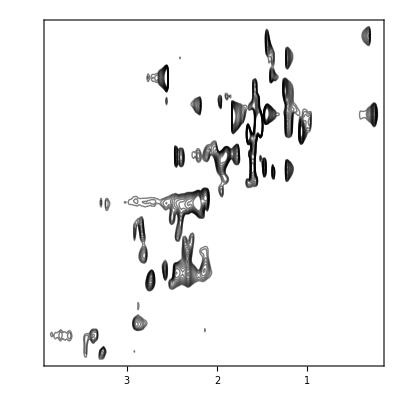

```mathematica
NMRContourPlot[Crop[spect,{{4.0,-.5},{50.0,5.0}}],Gain->5]
```